## DRS Project Team 4 | Air flow momentum analysis

We propose an equivalent dynamic system for which the forces produced by the air flow are transposed to the grounded revolute joint of the flap ( point 5).
Then we need to add a torque which is presented in “ An improved active drag reduction system for formula race cars ” 
from  Mauro Dimastrogiovanni, Giulio Reina and Andrea Burzoni.

With this approach the forces get balanced by the revolute joint and do not affect the dynamic evolution of the system any more.

Note that the results considered here are valid for any DRS configuration (push-up, rocker-pod, pull-pod).

-Graphics-

-Graphics-

Air flow speed taken from paper

```mathematica
vcdf = 50; (*[m/s]*)
```

Paper air-torque values

```mathematica
Tpaper = {{0,6.2},{10,6.2},{20,9.75},{30,9.2},{40,8},{50,5.2},{60,0.96},{70,-2.6}};
```

Scale the paper values for a vreal wanted air flow speed

-Graphics-

```mathematica
Ts = Tpaper*(vreal/vcdf)^2;
```

Extracted values for a give vreal

```mathematica
Tscaled = N@{{0,0.00248* vreal^2},{10,0.00248* vreal^2},{20,0.0039*vreal^2},{30,0.00368* vreal^2},{40,(2 vreal^2)/625},{50,0.0021* vreal^2},{60,0.000384* vreal^2},{70,-0.00104* vreal^2}}/.vreal->70 (*[m/s] = 252 [km/h]*)
```

{{0.,12.152},{10.,12.152},{20.,19.11},{30.,18.032},{40.,15.68},{50.,10.29},{60.,1.8816},{70.,-5.096}}

Second grade polynomial fit

```mathematica
FitPoly2 = Fit[Tscaled,{1,x,x^2},x]
```

10.8404+0.566393 x-0.011508 x^2

```mathematica
(* FitPloy3 = Fit[Mscaled,{1,x,x^2,x^3},x]
```

Plot both data and fit

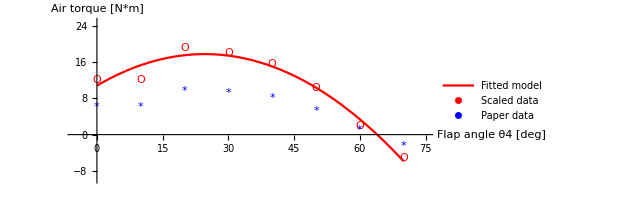

```mathematica
Show[
Plot[FitPoly2,{x,0,70},PlotStyle->Red,PlotRange->{{-5,75},{-10,25}},AspectRatio->{35/80},PlotLegends->{"Fitted model"},AxesLabel->{"Flap angle θ4 [deg]","Air torque [N*m]"}],
ListPlot[Tscaled,PlotStyle->Red,PlotMarkers->"O",PlotLegends->{"Scaled data"}],
ListPlot[Tpaper,PlotStyle->Blue,PlotMarkers->"*",PlotLegends->{"Paper data"}]
]
```

In the paper’s reference system (choice of θ4), it results that :
T_air(t) = 10.8404+0.566393 x-0.011508 x^2

Now we need to get this function for our reference systems.

### Push-up type

In this case the flap angle is θ2 and it’s set to 0 when the flap is horizontal and grows opposite to θ4 with a “bias” of deltaTheta = 113-70

```mathematica
PUdelta = 113-70
```

43

```mathematica
PUmodel =-(10.8404+0.566393 (x-PUdelta)-0.011508 (x-PUdelta)^2)
```

-10.8404-0.566393 (-43+x)+0.011508 (-43+x)^2

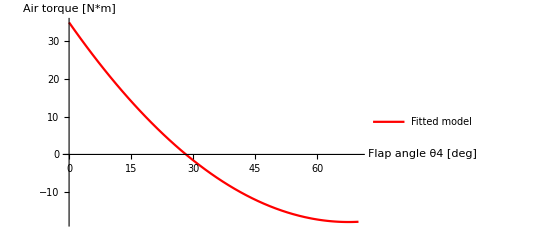

```mathematica
Plot[PUmodel,{x,0,70},PlotStyle->Red,PlotLegends->{"Fitted model"},AxesLabel->{"Flap angle θ4 [deg]","Air torque [N*m]"}]
```

### Rocker-pod type

### Pull-pod type